# Penrose Encoding and graph visualization.

## Diana Itzel Vázquez Santiago. Emmanuel Isaac Juárez Caballero. Jesús Eduardo Hermosilla Díaz. Maestría en Inteligencia Artificial, generación 2021-2023

## Initializing Cells

```mathematica
(*Starting Executing Cells*)
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
FindExternalEvaluators["Python"]
session=StartExternalSession["Python"]
```

ExternalSessionObject[…]

## Execution of the python code for the penrose Encoding.

```mathematica
NotebookDirectory[]
```

C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\

```mathematica
FileNames["*","C:\\Users\\emman\\OneDrive\\Documentos\\GitHub\\PenroseEncodingFinalProyect\\"]
```

{C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.git,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\.gitattributes,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\HTMLFiles,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\HTMLLinks,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\LICENSE,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\nuniversal.txt,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\penrose_encoding.py,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\README.md,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\Turing.html,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\Turing.nb,C:\Users\emman\OneDrive\Documentos\GitHub\PenroseEncodingFinalProyect\universal.txt}

```mathematica
u=Import["nuniversal.txt"]//ToExpression;
n=u;
ExternalEvaluate[session,File["penrose_encoding.py"]];
PenroseEncoding=ExternalEvaluate[session,"codificacion"];
execution=PenroseEncoding[50];
```

TM after Penrose Coding:  RR01R

Instructions from TM

0            00 -> 00R

1            01 -> 00R

2            10 -> 01R

## Pre-processing rules for the instructions that came from Penrose Encoding

```mathematica
MT=Import["universal.txt"];
```

```mathematica
MT=StringDelete[StringSplit[Text[MT]⟦1⟧,","],{"[","]","'", " "}];
```

## Visualization using Multigraph2 with modified elements (originally taken from: https://mathematica.stackexchange.com/questions/201183/how-to-get-distinct-labels-on-parallel-edges-in-a-graph)

### MultiGraph2 implementation: A tool to visualize correctly multilabel graphs on Wolfram Mathematica

```mathematica
ClearAll[multiGraph2]
multiGraph2[vl_,elist_,elabels_,estyles_,o:OptionsPattern[Graph]]:=Module[{esf,edges,labels,styles,sorted=Transpose@SortBy[Transpose[{elist,elabels,estyles}],{PositionIndex[vl]@#[[1,1]]&,PositionIndex[vl]@#[[1,2]]&}]},{edges,labels,styles}={sorted[[1]],##&@@(RotateRight/@sorted[[2;;]])};
esf={First[styles=RotateLeft[styles]],GraphElementData["Arrow", "ArrowSize"->0.01][##]/. Arrowheads[ah_]:>Arrowheads[Append[ah,{.0003,.7,Graphics[Text[Framed[First[labels=RotateLeft[labels]],FrameStyle->None,Background->White]]]}]]}&;
Graph[vl,edges,EdgeShapeFunction->esf,o]]
```

### Table generation for associations in the graph in order to be functional with multigraph2

```mathematica
fn=ParallelTable[{{FromDigits[(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ,2]},{FromDigits[((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin ),2]->FromDigits[((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin),2]},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```

### Visualization of the graph using Gravity Embedding, a method to visualize more clearly the graph.

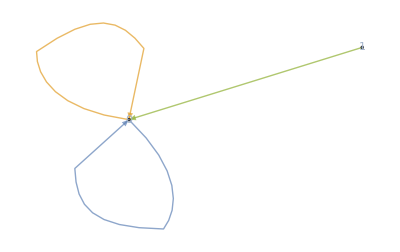

```mathematica
styles=ColorData[97]/@Range[Length[fn[[;;,3]]]];
multiGraph2[Flatten@Gather[(fn[[;;,1]]//Flatten)//DeleteDuplicates],fn[[;;,2]]//Flatten,fn[[;;,3]]//Flatten,styles,VertexSize->0.01,VertexLabels->Placed["Name",Center],ImageSize->Full, GraphLayout->"GravityEmbedding"]
```

## Past implementation (delete this at the end)

```mathematica
tabla3=ParallelTable[{{(StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin },{((StringSplit[MT[[i]],"->"][[1]]//Characters)[[1;;-2]]//StringJoin )->((StringSplit[MT[[i]],"->"][[2]]//Characters)[[;;-3]]//StringJoin)},{StringJoin[(StringSplit[MT[[i]],"->"][[1]]//Characters)//Last,(StringSplit[MT[[i]],"->"][[2]]//Characters)[[-2]],(StringSplit[MT[[i]],"->"][[2]]//Characters)//Last]}},{i,1,Length[MT]}];
```